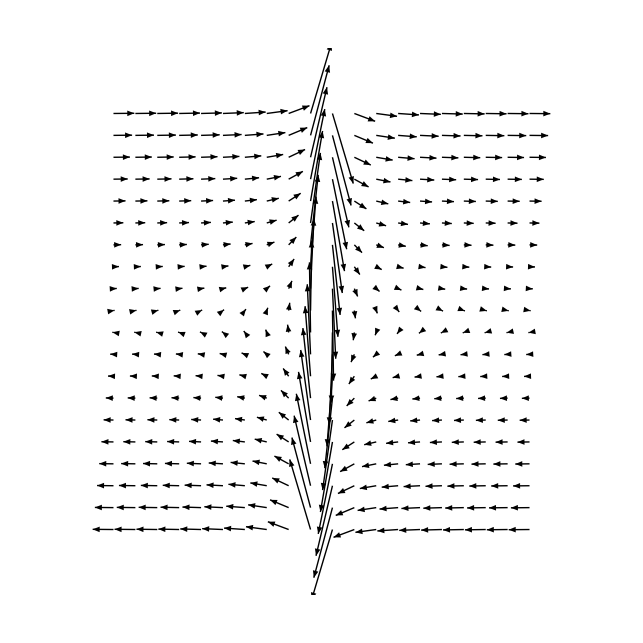

```mathematica
d=0.5;
d2=d/2;
Graphics[Map[Arrow[#]&,Flatten[Table[{{x,y},{x,y}+{y,-x/Abs[x]^3}/10},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1]],PlotRange->{{-6,6},{-6,6}}]
```

```mathematica
-D[-Exp[-x^2],x]
```

-2 ⅇ^(-x^2) x

```mathematica
d=0.4;
d2=d/2;
Graphics[Join[{Arrowheads[0.01]},Map[Arrow[#]&,Flatten[Table[{{x,y},{x,y}+{y,-2*x*Exp[-x^2]}/10},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1]]],PlotRange->{{-6,6},{-6,6}}]
Graphics[Join[{Arrowheads[0.01]},Map[Arrow[#]&,Flatten[Table[{{x,y},{x,y}+{y,-x/Abs[x]^3}/10},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1]]],PlotRange->{{-6,6},{-6,6}}]
```

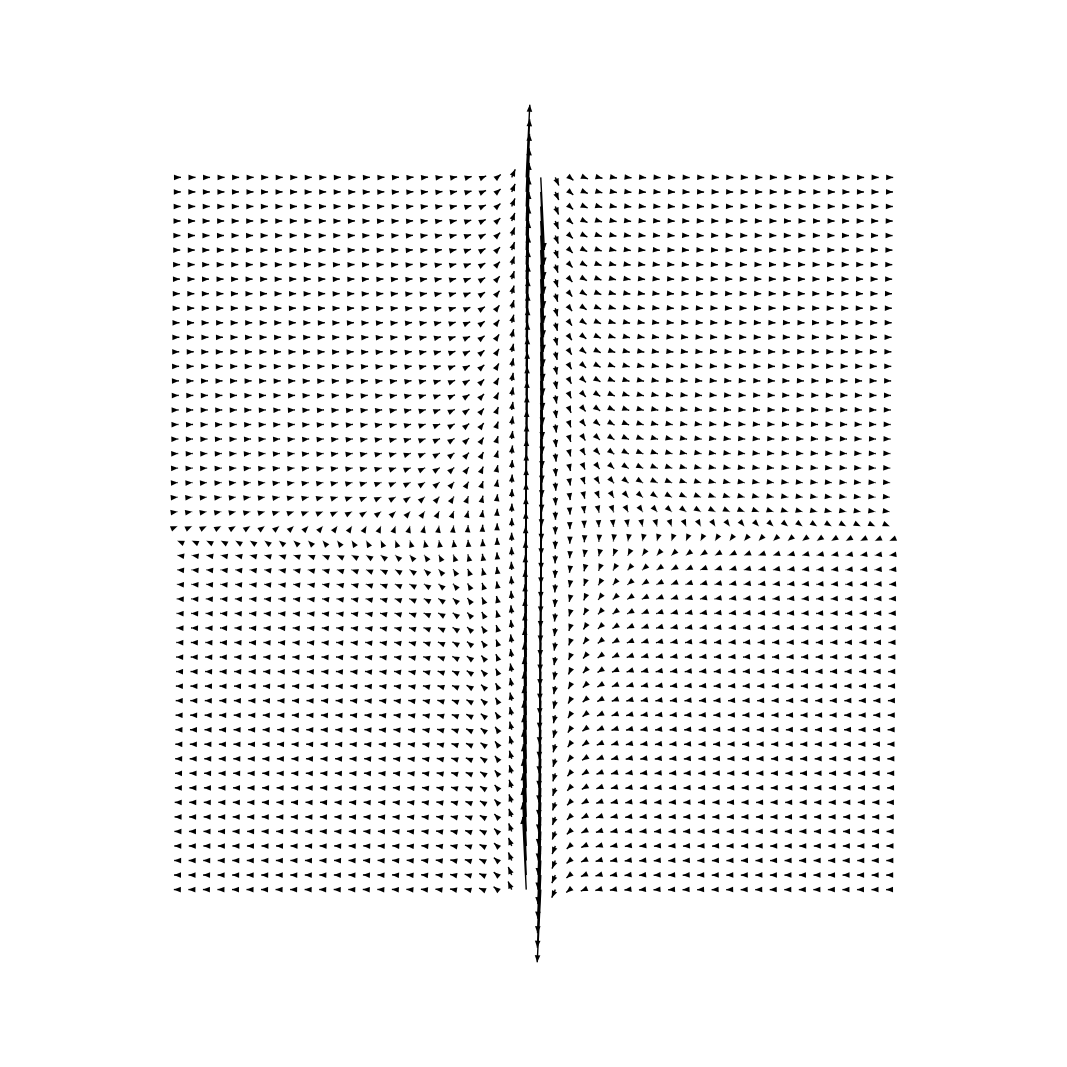

```mathematica
d=0.2;
d2=d/2;
Graphics[Join[{Arrowheads[0.01]},Map[Arrow[#]&,Flatten[Table[{{x,y},{x,y}+{y,-x/Abs[x]^3}/100},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1]]],PlotRange->{{-6,6},{-6,6}}]
```

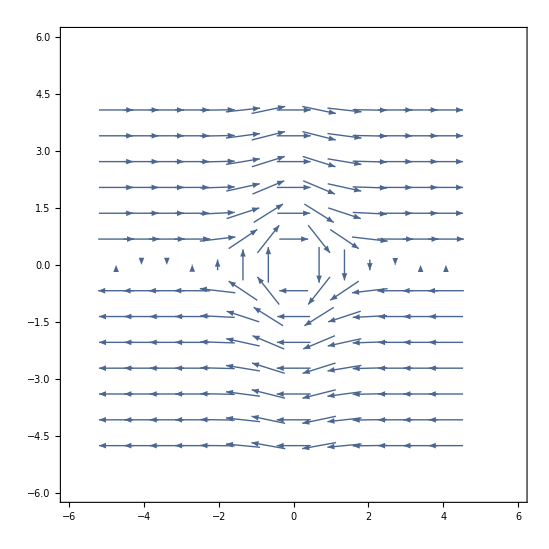

```mathematica
ListVectorPlot[Flatten[Table[{{x,y},Normalize@{y,-2*x*Exp[-x^2]}*10},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1],PlotRange->{{-6,6},{-6,6}}]
```

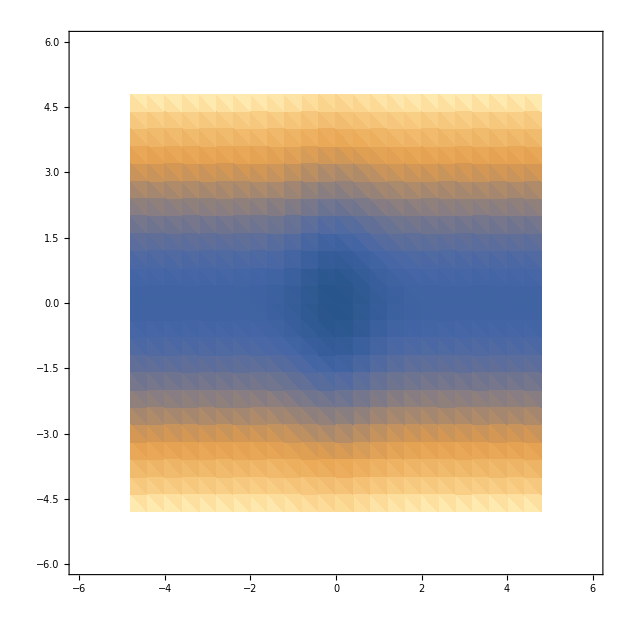

```mathematica
ListDensityPlot[Flatten[Table[{x,y,1/2*y^2-Exp[-x^2]},{x,-5+d2,5-d2,d},{y,-5+d2,5-d2,d}],1],PlotRange->{{-6,6},{-6,6}}]
```

```mathematica
Do[
v0=0.5*iv;
sol[iv]=NDSolve[{x'[t]==y[t],y'[t]==-2*x[t]*Exp[-x[t]^2],x[0]==0,y[0]==v0},{x,y},{t,0,10}, WorkingPrecision->40, MaxSteps->5000];
,{iv,-10,10}]
```

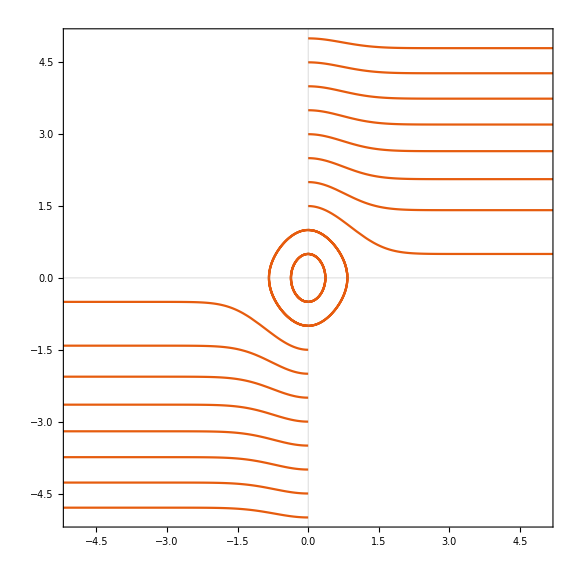

```mathematica
ParametricPlot[Table[{x[t],y[t]}/.sol[iv],{iv,-10,10}],{t,0,10},PlotRange->{{-5,5},{-5,5}},PlotTheme->"Scientific",ImageSize->Large]
```

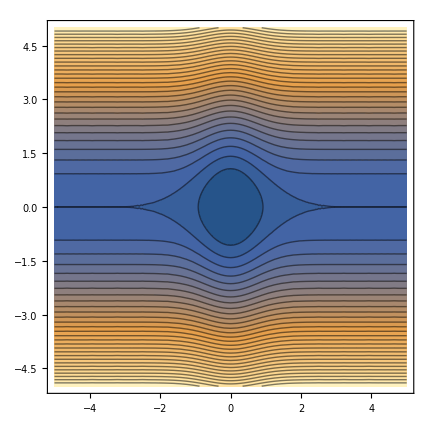

```mathematica
ContourPlot[1/2*y^2-Exp[-x^2],{x,-5,5},{y,-5,5},Contours->30]
```

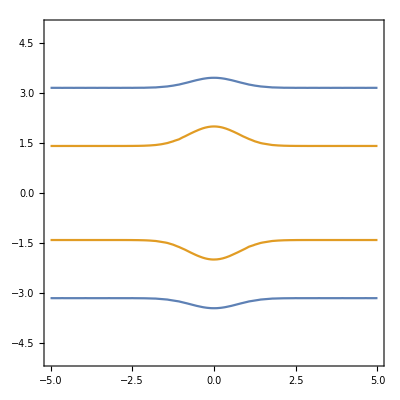

```mathematica
ContourPlot[{5==1/2*y^2-Exp[-x^2],1==1/2*y^2-Exp[-x^2]},{x,-5,5},{y,-5,5}]
```

```mathematica
sol[x_,H_]=y/.Solve[h==1/2*y^2-Exp[-x^2],y]/.h->H
```

{-√2 √(ⅇ^(-x^2)+H),√2 √(ⅇ^(-x^2)+H)}

```mathematica
dH=0.21;
dH2=dH/2;
H[iH_]:=-1+iH*dH2;

Table[e=H@iH,{iH,20}]
```

{-0.895,-0.79,-0.685,-0.58,-0.475,-0.37,-0.265,-0.16,-0.055,0.05,0.155,0.26,0.365,0.47,0.575,0.68,0.785,0.89,0.995,1.1}

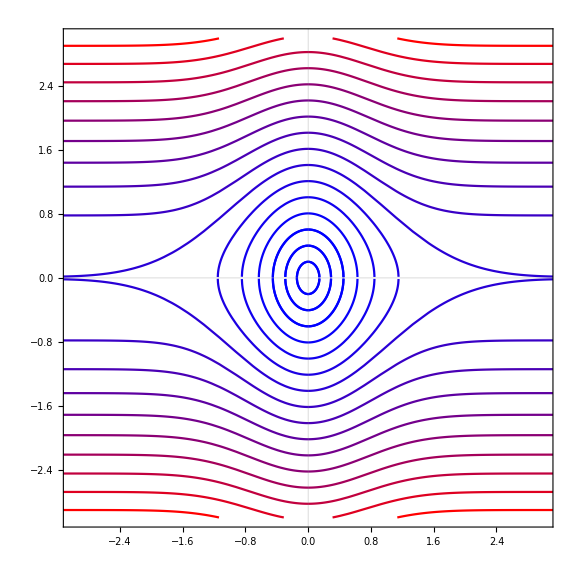

```mathematica
dH=0.04082;
dH2=dH/2;
H[iH_]:=-1+(-4+iH)^2*dH2;

Plot[Evaluate@Join[Table[e=H@iH;sol[x,e][[1]],{iH,20}],Table[e=H@iH;sol[x,e][[2]],{iH,20}]],{x,-5,5},PlotStyle->Table[e=H@iH;cv=(e-H[1])/(H[20]-H[1]);RGBColor[cv,0,1-cv],{iH,20}],PlotTheme->"Scientific",PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1]
```

```mathematica
qwertz=Plot[Evaluate@Join[Table[e=H@iH;sol[x,e][[1]],{iH,20}],Table[e=H@iH;sol[x,e][[2]],{iH,20}]],{x,-3,3},PlotStyle->Table[e=H@iH;cv=(e-H[1])/(H[20]-H[1]);RGBColor[cv,0,1-cv],{iH,20}],PlotTheme->"Scientific",PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1];
```

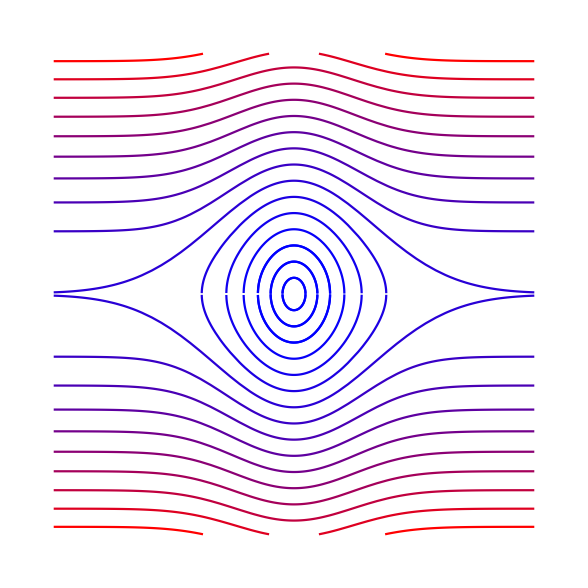

```mathematica
Graphics[qwertz[[1]]]
```

```mathematica
Export["/home/tm/Desktop/1.png",%233,"PNG"]
```

/home/tm/Desktop/1.png

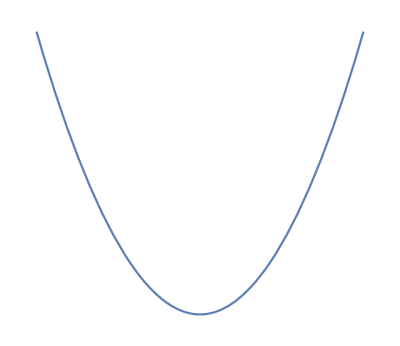

```mathematica
Graphics[Plot[x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1][[1]]]
```

```mathematica
FullForm[FullForm[Plot[x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1]][[1]]]
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-1.73111,3.],List[-1.65558,2.74094],List[-1.53904,2.36865],List[-1.4126,1.99543],List[-1.29462,1.67603],List[-1.16673,1.36125],List[-1.04118,1.08405],List[-0.924087,0.853937],List[-0.797091,0.635354],List[-0.795239,0.632405],List[-0.793387,0.629463],List[-0.789683,0.623599],List[-0.782274,0.611953],List[-0.767457,0.588991],List[-0.737824,0.544384],List[-0.678556,0.460439],List[-0.676549,0.457719],List[-0.674543,0.455008],List[-0.670529,0.449609],List[-0.662501,0.438908],List[-0.646446,0.417893],List[-0.614336,0.377409],List[-0.612329,0.374947],List[-0.610322,0.372493],List[-0.606308,0.36761],List[-0.598281,0.35794],List[-0.582226,0.338987],List[-0.550115,0.302627],List[-0.548145,0.300463],List[-0.546175,0.298307],List[-0.542234,0.294018],List[-0.534352,0.285533],List[-0.51859,0.268935],List[-0.487064,0.237231],List[-0.485094,0.235316],List[-0.483123,0.233408],List[-0.479183,0.229616],List[-0.471301,0.222125],List[-0.455538,0.207515],List[-0.424013,0.179787],List[-0.422175,0.178231],List[-0.420336,0.176683],List[-0.41666,0.173606],List[-0.409308,0.167533],List[-0.394602,0.155711],List[-0.365192,0.133365],List[-0.363354,0.132026],List[-0.361516,0.130694],List[-0.357839,0.128049],List[-0.350487,0.122841],List[-0.335782,0.112749],List[-0.306371,0.0938633],List[-0.304378,0.0926461],List[-0.302385,0.0914369],List[-0.298399,0.0890423],List[-0.290428,0.0843483],List[-0.274484,0.0753416],List[-0.272491,0.0742515],List[-0.270498,0.0731694],List[-0.266513,0.0710289],List[-0.258541,0.0668433],List[-0.242597,0.0588534],List[-0.240604,0.0578905],List[-0.238611,0.0569354],List[-0.234626,0.0550492],List[-0.226654,0.051372],List[-0.21071,0.0443988],List[-0.178823,0.0319778],List[-0.176963,0.0313158],List[-0.175102,0.0306607],List[-0.17138,0.0293713],List[-0.163938,0.0268755],List[-0.149052,0.0222164],List[-0.147191,0.0216652],List[-0.14533,0.0211209],List[-0.141609,0.020053],List[-0.134166,0.0180005],List[-0.11928,0.0142277],List[-0.117419,0.0137873],List[-0.115558,0.0133538],List[-0.111837,0.0125075],List[-0.104394,0.0108981],List[-0.102533,0.0105131],List[-0.100673,0.010135],List[-0.0969512,0.00939953],List[-0.0895082,0.00801173],List[-0.0876475,0.00768209],List[-0.0857868,0.00735937],List[-0.0820653,0.00673472],List[-0.0746224,0.0055685],List[-0.0727617,0.00529426],List[-0.0709009,0.00502694],List[-0.0671795,0.00451308],List[-0.0597365,0.00356845],List[-0.0579123,0.00335384],List[-0.0560882,0.00314588],List[-0.0524398,0.00274993],List[-0.0506156,0.00256194],List[-0.0487914,0.0023806],List[-0.045143,0.00203789],List[-0.0433188,0.00187652],List[-0.0414946,0.0017218],List[-0.0378462,0.00143234],List[-0.036022,0.00129759],List[-0.0341979,0.00116949],List[-0.0305495,0.00093327],List[-0.0287253,0.000825142],List[-0.0269011,0.000723668],List[-0.0250769,0.000628851],List[-0.0232527,0.000540688],List[-0.0214285,0.000459181],List[-0.0196043,0.000384329],List[-0.0177801,0.000316133],List[-0.0159559,0.000254592],List[-0.0141317,0.000199706],List[-0.0123076,0.000151476],List[-0.0104834,0.000109901],List[-0.00865917,0.0000749812],List[-0.00683498,0.0000467169],List[-0.00501079,0.000025108],List[-0.00318659,0.0000101544],List[-0.0013624,1.85614×10^-6],List[0.000461789,2.13249×10^-7],List[0.00228598,5.22571×10^-6],List[0.00411017,0.0000168935],List[0.00593436,0.0000352167],List[0.00775856,0.0000601952],List[0.00958275,0.000091829],List[0.0114069,0.000130118],List[0.0132311,0.000175063],List[0.0150553,0.000226663],List[0.0168795,0.000284918],List[0.0187037,0.000349829],List[0.0205279,0.000421395],List[0.0223521,0.000499616],List[0.0241763,0.000584493],List[0.0278247,0.000774212],List[0.0296489,0.000879055],List[0.031473,0.000990553],List[0.0351214,0.00123351],List[0.0369456,0.00136498],List[0.0387698,0.0015031],List[0.0424182,0.0017993],List[0.0442424,0.00195739],List[0.0460666,0.00212213],List[0.049715,0.00247158],List[0.0570117,0.00325034],List[0.0589907,0.0034799],List[0.0609697,0.0037173],List[0.0649276,0.0042156],List[0.0728436,0.00530618],List[0.0748225,0.00559841],List[0.0768015,0.00589847],List[0.0807595,0.00652209],List[0.0886754,0.00786332],List[0.0906544,0.00821821],List[0.0926333,0.00858094],List[0.0965913,0.00932988],List[0.104507,0.0109218],List[0.120339,0.0144815],List[0.122318,0.0149617],List[0.124297,0.0154497],List[0.128255,0.0164493],List[0.136171,0.0185425],List[0.152003,0.0231048],List[0.153982,0.0237104],List[0.155961,0.0243237],List[0.159919,0.025574],List[0.167835,0.0281684],List[0.183666,0.0337333],List[0.185513,0.0344151],List[0.18736,0.0351037],List[0.191053,0.0365014],List[0.198441,0.0393786],List[0.213215,0.0454605],List[0.215061,0.0462514],List[0.216908,0.0470492],List[0.220602,0.0486652],List[0.227989,0.0519789],List[0.242763,0.0589339],List[0.24461,0.059834],List[0.246457,0.0607409],List[0.25015,0.0625751],List[0.257537,0.0663255],List[0.272312,0.0741536],List[0.30186,0.0911194],List[0.303861,0.0923318],List[0.305863,0.0935522],List[0.309866,0.096017],List[0.317872,0.101043],List[0.333885,0.111479],List[0.36591,0.13389],List[0.367911,0.135359],List[0.369913,0.136836],List[0.373916,0.139813],List[0.381922,0.145865],List[0.397935,0.158352],List[0.42996,0.184865],List[0.431925,0.186559],List[0.43389,0.18826],List[0.43782,0.191686],List[0.44568,0.198631],List[0.4614,0.21289],List[0.49284,0.242892],List[0.555721,0.308826],List[0.557554,0.310866],List[0.559387,0.312914],List[0.563052,0.317028],List[0.570384,0.325338],List[0.585046,0.342279],List[0.614371,0.377452],List[0.673021,0.452958],List[0.675009,0.455637],List[0.676997,0.458325],List[0.680972,0.463723],List[0.688922,0.474614],List[0.704823,0.496776],List[0.736625,0.542616],List[0.800228,0.640365],List[0.918974,0.844513],List[1.03538,1.07201],List[1.16169,1.34953],List[1.27955,1.63724],List[1.40731,1.98051],List[1.5266,2.33052],List[1.64356,2.7013],List[1.73106,3.]]]],"Charting`Private`Tag$40677#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[0,0],List[0,0]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,1],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImageSize,Large],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-3,3],List[-3,3]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
ContourPlot[{5==1/2*y^2-Exp[-x^2],1==1/2*y^2-Exp[-x^2]},{x,-5,5},{y,-5,5}]
```

-Graphics-

```mathematica
sol[x_,H_]=y/.Solve[h==1/2*y^2-Exp[-x^2],y]/.h->H
```

{-√2 √(ⅇ^(-x^2)+H),√2 √(ⅇ^(-x^2)+H)}

```mathematica
(* dH=0.21;
dH2=dH/2;
H[iH_]:=-1+iH*dH2;

Table[H@iH,{iH,20}] *)
```

{-0.895,-0.79,-0.685,-0.58,-0.475,-0.37,-0.265,-0.16,-0.055,0.05,0.155,0.26,0.365,0.47,0.575,0.68,0.785,0.89,0.995,1.1}

```mathematica
sol[0,H@iH]
```

{0.+1.27774 ⅈ,0.+1.35526 ⅈ,0.+1.39971 ⅈ,0.+1.41421 ⅈ,0.+1.39971 ⅈ,0.+1.35526 ⅈ,0.+1.27774 ⅈ,0.+1.16055 ⅈ,0.+0.989697 ⅈ,0.+0.728341 ⅈ,0.0134164,0.782611,1.14299,1.44291,1.71442,1.96928,2.21327,2.44964,2.68039,2.90687}

```mathematica
Solv1/2*y^2-Exp[-x^2]
```

{-0.81631,-0.91836,-0.97959,-1.,-0.97959,-0.91836,-0.81631,-0.67344,-0.48975,-0.26524,0.00009,0.30624,0.65321,1.041,1.46961,1.93904,2.44929,3.00036,3.59225,4.22496}

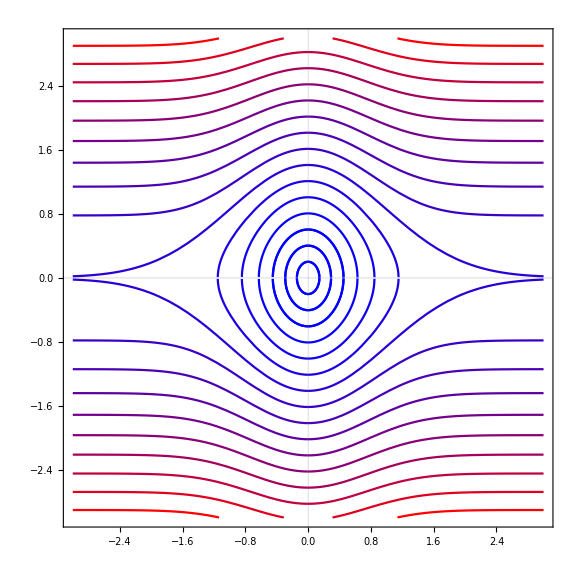

```mathematica
dH=0.04082;
dH2=dH/2;
H[iH_]:=-1+(-4+iH)^2*dH2;
Table[H@iH,{iH,20}]

Plot[Evaluate@Join[Table[e=H@iH;sol[x,e][[1]],{iH,20}],Table[e=H@iH;sol[x,e][[2]],{iH,20}]],{x,-3,3},PlotStyle->Table[e=H@iH;cv=(e-H[1])/(H[20]-H[1]);RGBColor[cv,0,1-cv],{iH,20}],PlotTheme->"Scientific",PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1]
```

```mathematica
qwertz=Plot[Evaluate@Join[Table[e=H@iH;sol[x,e][[1]],{iH,20}],Table[e=H@iH;sol[x,e][[2]],{iH,20}]],{x,-3,3},PlotStyle->Table[e=H@iH;cv=(e-H[1])/(H[20]-H[1]);RGBColor[cv,0,1-cv],{iH,20}],PlotTheme->"Scientific",PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1];
```

```mathematica
Graphics[qwertz[[1]]]
```

-Graphics-

```mathematica
Export["/home/tm/Desktop/1.png",%233,"PNG"]
```

/home/tm/Desktop/1.png

```mathematica
Graphics[Plot[x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1][[1]]]
```

-Graphics-

```mathematica
FullForm[FullForm[Plot[x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}},ImageSize->Large,AspectRatio->1]][[1]]]
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-1.73111,3.],List[-1.65558,2.74094],List[-1.53904,2.36865],List[-1.4126,1.99543],List[-1.29462,1.67603],List[-1.16673,1.36125],List[-1.04118,1.08405],List[-0.924087,0.853937],List[-0.797091,0.635354],List[-0.795239,0.632405],List[-0.793387,0.629463],List[-0.789683,0.623599],List[-0.782274,0.611953],List[-0.767457,0.588991],List[-0.737824,0.544384],List[-0.678556,0.460439],List[-0.676549,0.457719],List[-0.674543,0.455008],List[-0.670529,0.449609],List[-0.662501,0.438908],List[-0.646446,0.417893],List[-0.614336,0.377409],List[-0.612329,0.374947],List[-0.610322,0.372493],List[-0.606308,0.36761],List[-0.598281,0.35794],List[-0.582226,0.338987],List[-0.550115,0.302627],List[-0.548145,0.300463],List[-0.546175,0.298307],List[-0.542234,0.294018],List[-0.534352,0.285533],List[-0.51859,0.268935],List[-0.487064,0.237231],List[-0.485094,0.235316],List[-0.483123,0.233408],List[-0.479183,0.229616],List[-0.471301,0.222125],List[-0.455538,0.207515],List[-0.424013,0.179787],List[-0.422175,0.178231],List[-0.420336,0.176683],List[-0.41666,0.173606],List[-0.409308,0.167533],List[-0.394602,0.155711],List[-0.365192,0.133365],List[-0.363354,0.132026],List[-0.361516,0.130694],List[-0.357839,0.128049],List[-0.350487,0.122841],List[-0.335782,0.112749],List[-0.306371,0.0938633],List[-0.304378,0.0926461],List[-0.302385,0.0914369],List[-0.298399,0.0890423],List[-0.290428,0.0843483],List[-0.274484,0.0753416],List[-0.272491,0.0742515],List[-0.270498,0.0731694],List[-0.266513,0.0710289],List[-0.258541,0.0668433],List[-0.242597,0.0588534],List[-0.240604,0.0578905],List[-0.238611,0.0569354],List[-0.234626,0.0550492],List[-0.226654,0.051372],List[-0.21071,0.0443988],List[-0.178823,0.0319778],List[-0.176963,0.0313158],List[-0.175102,0.0306607],List[-0.17138,0.0293713],List[-0.163938,0.0268755],List[-0.149052,0.0222164],List[-0.147191,0.0216652],List[-0.14533,0.0211209],List[-0.141609,0.020053],List[-0.134166,0.0180005],List[-0.11928,0.0142277],List[-0.117419,0.0137873],List[-0.115558,0.0133538],List[-0.111837,0.0125075],List[-0.104394,0.0108981],List[-0.102533,0.0105131],List[-0.100673,0.010135],List[-0.0969512,0.00939953],List[-0.0895082,0.00801173],List[-0.0876475,0.00768209],List[-0.0857868,0.00735937],List[-0.0820653,0.00673472],List[-0.0746224,0.0055685],List[-0.0727617,0.00529426],List[-0.0709009,0.00502694],List[-0.0671795,0.00451308],List[-0.0597365,0.00356845],List[-0.0579123,0.00335384],List[-0.0560882,0.00314588],List[-0.0524398,0.00274993],List[-0.0506156,0.00256194],List[-0.0487914,0.0023806],List[-0.045143,0.00203789],List[-0.0433188,0.00187652],List[-0.0414946,0.0017218],List[-0.0378462,0.00143234],List[-0.036022,0.00129759],List[-0.0341979,0.00116949],List[-0.0305495,0.00093327],List[-0.0287253,0.000825142],List[-0.0269011,0.000723668],List[-0.0250769,0.000628851],List[-0.0232527,0.000540688],List[-0.0214285,0.000459181],List[-0.0196043,0.000384329],List[-0.0177801,0.000316133],List[-0.0159559,0.000254592],List[-0.0141317,0.000199706],List[-0.0123076,0.000151476],List[-0.0104834,0.000109901],List[-0.00865917,0.0000749812],List[-0.00683498,0.0000467169],List[-0.00501079,0.000025108],List[-0.00318659,0.0000101544],List[-0.0013624,1.85614×10^-6],List[0.000461789,2.13249×10^-7],List[0.00228598,5.22571×10^-6],List[0.00411017,0.0000168935],List[0.00593436,0.0000352167],List[0.00775856,0.0000601952],List[0.00958275,0.000091829],List[0.0114069,0.000130118],List[0.0132311,0.000175063],List[0.0150553,0.000226663],List[0.0168795,0.000284918],List[0.0187037,0.000349829],List[0.0205279,0.000421395],List[0.0223521,0.000499616],List[0.0241763,0.000584493],List[0.0278247,0.000774212],List[0.0296489,0.000879055],List[0.031473,0.000990553],List[0.0351214,0.00123351],List[0.0369456,0.00136498],List[0.0387698,0.0015031],List[0.0424182,0.0017993],List[0.0442424,0.00195739],List[0.0460666,0.00212213],List[0.049715,0.00247158],List[0.0570117,0.00325034],List[0.0589907,0.0034799],List[0.0609697,0.0037173],List[0.0649276,0.0042156],List[0.0728436,0.00530618],List[0.0748225,0.00559841],List[0.0768015,0.00589847],List[0.0807595,0.00652209],List[0.0886754,0.00786332],List[0.0906544,0.00821821],List[0.0926333,0.00858094],List[0.0965913,0.00932988],List[0.104507,0.0109218],List[0.120339,0.0144815],List[0.122318,0.0149617],List[0.124297,0.0154497],List[0.128255,0.0164493],List[0.136171,0.0185425],List[0.152003,0.0231048],List[0.153982,0.0237104],List[0.155961,0.0243237],List[0.159919,0.025574],List[0.167835,0.0281684],List[0.183666,0.0337333],List[0.185513,0.0344151],List[0.18736,0.0351037],List[0.191053,0.0365014],List[0.198441,0.0393786],List[0.213215,0.0454605],List[0.215061,0.0462514],List[0.216908,0.0470492],List[0.220602,0.0486652],List[0.227989,0.0519789],List[0.242763,0.0589339],List[0.24461,0.059834],List[0.246457,0.0607409],List[0.25015,0.0625751],List[0.257537,0.0663255],List[0.272312,0.0741536],List[0.30186,0.0911194],List[0.303861,0.0923318],List[0.305863,0.0935522],List[0.309866,0.096017],List[0.317872,0.101043],List[0.333885,0.111479],List[0.36591,0.13389],List[0.367911,0.135359],List[0.369913,0.136836],List[0.373916,0.139813],List[0.381922,0.145865],List[0.397935,0.158352],List[0.42996,0.184865],List[0.431925,0.186559],List[0.43389,0.18826],List[0.43782,0.191686],List[0.44568,0.198631],List[0.4614,0.21289],List[0.49284,0.242892],List[0.555721,0.308826],List[0.557554,0.310866],List[0.559387,0.312914],List[0.563052,0.317028],List[0.570384,0.325338],List[0.585046,0.342279],List[0.614371,0.377452],List[0.673021,0.452958],List[0.675009,0.455637],List[0.676997,0.458325],List[0.680972,0.463723],List[0.688922,0.474614],List[0.704823,0.496776],List[0.736625,0.542616],List[0.800228,0.640365],List[0.918974,0.844513],List[1.03538,1.07201],List[1.16169,1.34953],List[1.27955,1.63724],List[1.40731,1.98051],List[1.5266,2.33052],List[1.64356,2.7013],List[1.73106,3.]]]],"Charting`Private`Tag$40677#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]],List[Automatic,Charting`ScaledFrameTicks[List[Identity,Identity]]]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[0,0],List[0,0]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,1],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImageSize,Large],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-3,3],List[-3,3]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[Ticks,List[Automatic,Automatic]]]]